# multi-qubit gates

P. Huft 

Todo: put my quantum functions into a package. could also port to python as part of my AMO ecosphere.

## functions

```mathematica
(*FUNCTIONS*)
OuterProd[A_,B_]:=Outer[Times,A,B]; (*outer product of vectors or matrices A,B*)
HamiltonianProduct[hsingle_,volume_ ]:=Module[
{totalham=hsingle},
(*the Hamiltonian describing the combined space of `volume` number of quantum systems with individual Hamiltonian hsingle*)
For[i=1,i<volume,i++,
totalham = KroneckerProduct[IdentityMatrix[Length[hsingle]],totalham] + KroneckerProduct[hsingle,IdentityMatrix[Length[totalham]]];
];
totalham
];
(*the total shift to an n-atom state due to an interaction between the atoms participating*)
InteractionTerm[atomIdcs_,blockadeTwoAtoms_]:=Total[Flatten@Table[blockadeTwoAtoms[atomIdcs[[i]],atomIdcs[[j]]],{i,Range[Length[atomIdcs]]},{j,Range[1+i,Length[atomIdcs]]}]]
BlockadeHamiltonian[atomNum_,blockade_]:=Module[
{excitedList={0,1},n,HBlockade},
(*blockade is a function that takes a list of atom indices (1,2...) and return the corresponding blockade between atoms*)

(*generate list of Rydberg-excited atoms at each index of the basis. for now, this assumes a system of two-level atoms*)
For[i=1,i<atomNum,i++,
n=(Flatten@excitedList)[[-1]]+1;
AppendTo[excitedList,n];
oldLength = Length[excitedList];
For[j=2,j<oldLength,j++,
AppendTo[excitedList,Flatten@{excitedList[[j]],n}];
];
];

dim = 2^atomNum;
HBlockade = ConstantArray[0,{dim,dim}];
For[k=1,k<dim+1,k++,
atoms = excitedList[[k]];
HBlockade[[k,k]]=If[Length[atoms]>0,blockade[atoms],0];
];
HBlockade
];
ΩBString[i_,j_]:=StringForm["Ω_B^(``, ``)",i,j];
BuildMasterEq[ρ0_,H_]:=Module[{dim,rho,eqIdcs,comm,linblad,rhoPruned,eqsPruned,rhoICPruned, popIdxList, cohIdxList},
(*The junk below just builds the eqs to be passed to NDSolve, removing the redundant matrix elements. The derivatives could be worked out explicitly and typed in (just the optical Bloch equations) but this can do the heavy lifting for higher than 2-dimensional systems.

"Pruned" variables refer to the eqs which have had the redundant element removed

Args: ρ0, the initial density matrix; H, the Hamiltonian
Returns: eqsPruned, rhoICPruned (the pruned initial state), rhoPruned (the pruned set of variables, i.e. elements of ρ, to solve for), popIdxList (the indices of the population terms), cohIdxList (inds of the coherence terms)
*)
Clear[ρ,t];
dim = Length[H];
rho=Array[Subscript[ρ, #1,#2][t](*[#1,#2][t]*)&,{dim,dim}];
(*enforce conjugate relationship of ρ's off-diagonals *)
eqIdcs = {};
For[i=1,i<dim+1,i++,
For[j=dim,j>i,j--,
rho[[j,i]] = Conjugate[rho[[i,j]]];
AppendTo[eqIdcs,{i,j}]
]
];
(*generate non-redundant eqs and initial conditions*)
comm = rho.H - H.rho ;
(*linblad =Γ(σm.rho.σp-1/2((σp.σm).rho + rho.(σp.σm)));*)
rhoPruned ={};
eqsPruned = {};
rhoICPruned = {};
For[i=1,i<dim+1,i++,
For[j=1,j<dim+1,j++,
If[i<=j,
AppendTo[eqsPruned,D[rho[[i,j]],t]==-ⅈ comm[[i,j]]];(*+linblad[[i,j]]];*)
AppendTo[rhoICPruned,(rho/.t-> 0)[[i,j]]==ρ0[[i,j]]];
AppendTo[rhoPruned,rho[[i,j]]]
];
];
];
(*generate indices for population and coherence terms in pruned eq list*)
popIdxList ={1};
cohIdxList = {};
j=0;
last = 1;
elems = dim(dim+1)/2;
For[i=1,i<elems,i++
If[i ==last+dim-j,
{AppendTo[popIdxList,i],last=i,j++},
AppendTo[cohIdxList,i]
]
];
{eqsPruned,rhoICPruned,rhoPruned, popIdxList, cohIdxList}
];
```

## gate construction

build single and multi-qubit gates out of local and global qubit operations.

can express gates as rotation matrices acting on one or may qubits, but not clear how to use this way of expressing gates to compute something like a parity oscillation. that time dependent dynamic is found by evolving the system from the Hamiltonian, which is not represented in terms of the rotation operators

```mathematica
(*single qubits*)
R[θ_,ϕ_] = ({{0, Ω}, {Ω, 0}})
```

## cnot

## ghz states

```mathematica
Clear[Ω,Δ];
numQubits= 2;
qubitBasis = IdentityMatrix[2];
Hsingle=({{0, Ω/2}, {Ω/2, Δ}});(*assume real Rabi freq.*)
(*Hint = ConstantArray[0,{2 numQubits ,2numQubits}];
Hint[[2numQubits ,2numQubits]]=Ωint; *)
Hqubits=HamiltonianProduct[Hsingle,numQubits];
Ω=2π;
Ωint  = 100 Ω;
Δ=0;
tmax = 1;
ρ0 = ({{1/2, 0, 0, 1/2}, {0, 0, 0, 0}, {0, 0, 0, 0}, {1/2, 0, 0, 1/2}});
(*build the equations*)
{eqs,IC, rho,popIdcs,cohIdcs}=BuildMasterEq[ρ0,H];
(*solve for the time evolution*)
{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,IC], rho, {t,0,tmax}]];
Print["Time to run sim: ",time];
(*build a plot of the elements*)
curves={};
(*labels ={"ρ00","|ρ01|","ρ11"};*)
For[i=1, i<Length[soln]+1,i++,
AppendTo[curves,Abs[soln[[i,2]]]]
];
```

## tests

```mathematica
(*single qubit Hamiltonian with effective basis {0,1}*)
Clear[Ω,Δ];
numQubits= 2;
qubitBasis = IdentityMatrix[numStates];
Hsingle=({{0, Ω/2}, {Ω/2, Δ}});(*assume real Rabi freq.*)
Hint = ConstantArray[0,{2 numQubits ,2numQubits}];
Hint[[2numQubits ,2numQubits]]=Ωint; 
Hqubits=HamiltonianProduct[Hsingle,numQubits];
```

```mathematica
H=Hqubits+Hint;
H//MatrixForm
```

(0 | Ω/2 | Ω/2 | 0
Ω/2 | Δ | 0 | Ω/2
Ω/2 | 0 | Δ | Ω/2
0 | Ω/2 | Ω/2 | 2 Δ+Ωint)

Time to run sim: 0.015625

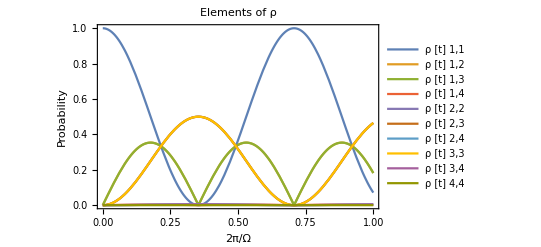

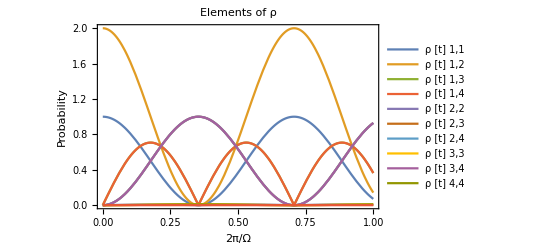

```mathematica
(*Rabi oscillations with a strong interaction preventing double excitation, 
e.g. Rydberg-blockade*)

Ω=2π;
Ωint  = 100 Ω;
Δ=0;
tmax = 1;
ρ0 = ({{1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
(*build the equations*)
{eqs,IC, rho,popIdcs,cohIdcs}=BuildMasterEq[ρ0,H];
(*solve for the time evolution*)
{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,IC], rho, {t,0,tmax}]];
Print["Time to run sim: ",time];
(*build a plot of the elements*)
curves={};
(*labels ={"ρ00","|ρ01|","ρ11"};*)
For[i=1, i<Length[soln]+1,i++,
AppendTo[curves,Abs[soln[[i,2]]]]
];

(*plot the populations and coherence*)
labels = Array[ToString[rho[[#]]]&,Length[rho]];
Plot[Evaluate[curves], {t, 0, tmax},PlotRange->All,PlotLegends->labels,Axes-> Off,Frame-> {True,True,False,False},FrameLabel-> {"2π/Ω","Probability"},PlotLabel->"Elements of ρ"]

(*plot ground state and singly-excited Rydberg state*)
curvesGroundRyd=Join@{curves[[1]],(curves[[5]]+curves[[9]])};
Plot[Evaluate[curvesGroundRyd], {t, 0, tmax},PlotRange->All,PlotLegends->labels,Axes-> Off,Frame-> {True,True,False,False},FrameLabel-> {"2π/Ω","Probability"},PlotLabel->"Elements of ρ"]
```

```mathematica
rho
```

{ρ_(1,1)[t],ρ_(1,2)[t],ρ_(1,3)[t],ρ_(1,4)[t],ρ_(2,2)[t],ρ_(2,3)[t],ρ_(2,4)[t],ρ_(3,3)[t],ρ_(3,4)[t],ρ_(4,4)[t]}